# Derivative

## Function

```mathematica
f[x_]=TriangleWave[x](x-1);
```

Point

```mathematica
Subscript[x, 1]=1/4;
```

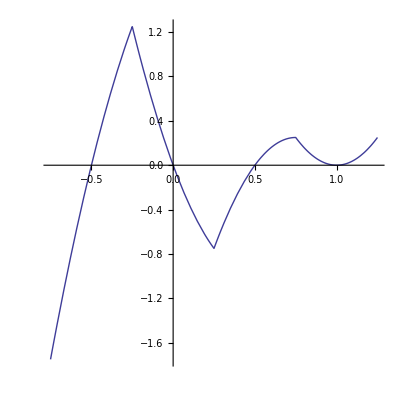

```mathematica
Plot[f[x],{x,Subscript[x, 1]-1,Subscript[x, 1]+1},AspectRatio->1]
```

## Left derivative :

```mathematica
Limit[(f[Subscript[x, 1]+Δx]-f[Subscript[x, 1]])/Δx,Δx->0,Direction->1]
```

-2

## Right derivative :

```mathematica
Limit[(f[Subscript[x, 1]+Δx]-f[Subscript[x, 1]])/Δx,Δx->0,Direction->-1]
```

4